```mathematica
data=ReadList["C:\\Users\\machaoqun\\Desktop\\mlr_matrix2301","Record"];
```

```mathematica
d=StringSplit[#," "]&/@data;
```

```mathematica
d//Length
```

2400

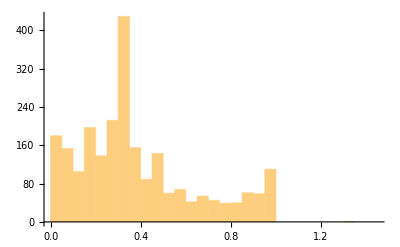

```mathematica
d[[All,1]]//ToExpression//Histogram
```